```mathematica
<<"http://www.physics.wisc.edu/~tgwalker/448defs.m"
```

```mathematica
Subscript[P, 1,0][r]
```

2 ⅇ^-r r

```mathematica
Integrate[(Subscript[P, 1,0][r])^2,{r,0,∞}]
```

1

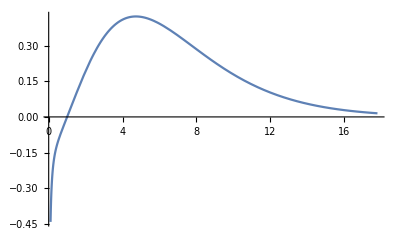

```mathematica
Plot[Subscript[P, 2.11,1][r],{r,.1,4 2.11^2},PlotRange->All]
```

```mathematica
NIntegrate[(Subscript[P, 1.62,0][r])^2,{r,0,20}]
```

0.996779

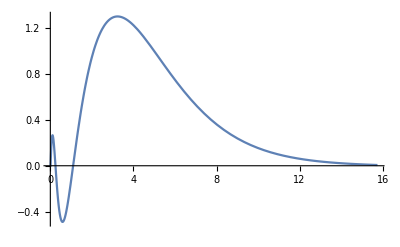

```mathematica
With[{rout=6 1.62^2},sol=NDSolve[{-1/2 p''[s]-(10 ⅇ^(-1.9s)+1)/s p[s]==-1/(2 1.62^2)p[s],p[rout]==1,p'[rout]==-1},p,{s,rout,.01}]⟦1,1,2⟧;
Plot[sol[s]/sol[5],{s,.01,rout}]]
```

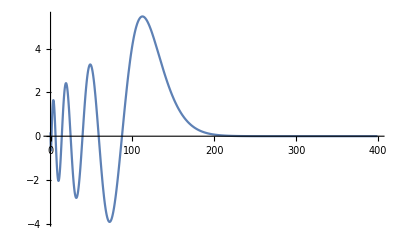

```mathematica
Module[{nstar=8.16,rout,l=1},rout=6 nstar^2;sol=NDSolve[{-1/2 p''[s]-(10 ⅇ^(-2.4s)+1)/s p[s]+(l(l+1))/(2 s^2)p[s]==-1/(2 nstar^2)p[s],p[rout]==1,p'[rout]==-1},p,{s,rout,.01}]⟦1,1,2⟧;
Plot[sol[s]/sol[5],{s,.01,rout}]]
```

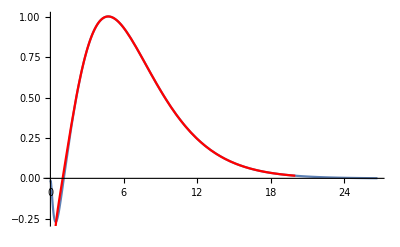

```mathematica
Show[%30,Plot[ (Subscript[P, 2.11,1][r])/(Subscript[P, 2.11,1][5]),{r,.1,20},PlotStyle->Red]]
```

```mathematica
1/(√(2(.1888-{.0773,.1379})))
```

{2.11762,3.1342}

```mathematica
NIntegrate[Subscript[P, 1.62,0][r]Subscript[P, 2.11,1][r]r,{r,0,∞}]
```

4.22854

```mathematica
?P
```

```mathematica
sol[2]
```

InterpolatingFunction[…][s][2]

```mathematica
.1888-.1513
```

0.0375

```mathematica
√(1/(.0375 2))
```

3.65148